```mathematica
data = Table[{x,Sin[x]+Random[Real,{-1,1}]},{x,-5,5,0.25}]
```

{{-5.,0.748835},{-4.75,0.58281},{-4.5,0.205633},{-4.25,0.814932},{-4.,0.39372},{-3.75,0.291741},{-3.5,0.945985},{-3.25,-0.0619914},{-3.,-0.370575},{-2.75,-0.317723},{-2.5,-1.11452},{-2.25,-0.463192},{-2.,-0.935231},{-1.75,-1.12546},{-1.5,-1.13903},{-1.25,-1.77312},{-1.,-0.906887},{-0.75,-0.120586},{-0.5,0.0480819},{-0.25,-0.617805},{0.,-0.333997},{0.25,-0.0528866},{0.5,0.694027},{0.75,0.0993299},{1.,1.71756},{1.25,0.0651769},{1.5,0.983993},{1.75,1.48173},{2.,1.14847},{2.25,1.17409},{2.5,0.989769},{2.75,0.0495961},{3.,-0.39025},{3.25,-0.776121},{3.5,-0.443438},{3.75,-0.218508},{4.,-0.262238},{4.25,-0.421441},{4.5,-1.92865},{4.75,-0.822106},{5.,-1.39894}}

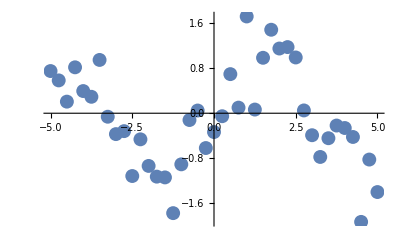

```mathematica
pointplot = ListPlot[data,PlotStyle->PointSize[0.025]]
```

```mathematica
poly15fit = Fit[data,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8,x^9,x^10,x^11,x^12,x^13,x^14,x^15},x]
```

0.0594498+0.845373 x-0.614115 x^2-0.137173 x^3+0.467743 x^4+0.0831125 x^5-0.123327 x^6-0.0270037 x^7+0.014923 x^8+0.00353251 x^9-0.000908037 x^10-0.000220597 x^11+0.0000270422 x^12+6.6162×10^-6 x^13-3.13628×10^-7 x^14-7.67662×10^-8 x^15

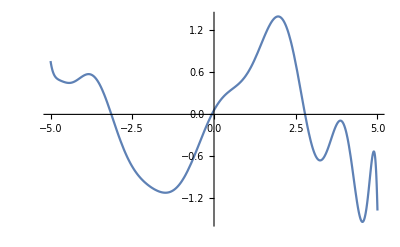

```mathematica
poly15plot = Plot[poly15fit,{x,-5,5}]
```